```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,

(*Newman - Specified Load*)
(*For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];*)
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];

];

];
{kglob,fglob}
]
```

```mathematica
(*Calcula as funções psi as coordenas x e y, o gradiente de psi e o jacobiano *)
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta,co,dx,dy},
(*psis=GeneratePsis[order];*)
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas
]
```

```mathematica
(*Calcula a contribuição da equação diferencial do problema de elasticidade (ek e ef) em cada ponto de integração *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},

{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
InvJac=Inverse[Jac];
DetJ=Det[Jac];
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

fu=-1;
For[i=1,i≤ nnodes,i++,

ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];

{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order];
intpts=Length[intrule];
If[order==1,
nnodes=4  ;
];
If[order==2,
nnodes=9;
];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];
Print["elcoords = ",elcoords];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,topol_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},

p=order;
nels=Length[allcoords];
(*nnodes=Length[allcoords] order;*)
sz= Length[nnodes]2;
If[order==1,
rows=4  ;
];
If[order==2,
rows=9;
];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];

For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiffElastic[order,co];
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineNewman[EF_,fx_,order_,nodes_,topol_,id1_,id2_,fxorfy_]:=Block[{k,Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,vecnodes,iel,vecids={},id={},idy},
iel=Length[topol];
vecnodes={};

If[fxorfy==1,(*fy*)
fi=0;
idy=2;
];
If[fxorfy==0,(*fx*)
fi=-1;
idy=1;
];
If[order==1,
k=4;
];
If[order==2,
k=9;
];

For[j=1,j≤iel,j++,
node={};
id={};
For[i=1,i≤k,i++,
If[nodes[[ topol[[j,i]] ]][[idy]]==nodes[[id1]][[idy]],
AppendTo[node,nodes[[ topol[[j,i]] ]]];
AppendTo[id,topol[[j,i]]];
];
];
If[Length[node]≠0,
node=SortBy[node,Small];
AppendTo[vecnodes,node];
If[order==1,
id=Sort[id,Greater];
];
If[order==2,
id=Sort[id];
id=Sort[id,Greater];
];
AppendTo[vecids,id];
];
];

(*Print["vecnodes = ",vecnodes];
Print["vecids = ",vecids];*)
el=Length[vecnodes];
{elsw,ids}=DefineLineNodes[id1,id2,nodes];
(*Print["ids = ",ids];
Print["iel = ",el];*)

For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co=vecnodes[[i]];
Print["co = ",co];
newco=co;
xx=Sum[shapes[[i]] newco[[i]][[1]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
(*Print["vecids[[i]]= ",vecids[[i]]];
Print["integralxi1= ",integralxi1];*)
If[order==1,
Ef[[ vecids[[i,1]] 2+fi]]+=integralxi1[[1]];
Ef[[ vecids[[i,2]] 2+fi]]+=integralxi1[[2]];
];
If[order==2,
(*Print["vecids[[i,1]] 2 = ",vecids[[i,1]] 2+fi];
Print["vecids[[i,2]] 2 = ",vecids[[i,2]] 2+fi];
Print["vecids[[i,3]] 2 = ",vecids[[i,3]] 2+fi];
Print["integralxi1[[1]]  = ",integralxi1[[1]]];*)
Ef[[vecids[[i,1]] 2+fi]]+=integralxi1[[1]];
Ef[[ vecids[[i,2]] 2+fi]]+=integralxi1[[2]];
Ef[[ vecids[[i,3]] 2+fi]]+=integralxi1[[3]];
];

];
Ef
];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];
nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
For[i=1,i≤nels,i++,

x=0.;
y=0.;

If[order==1,
kk=4;
];
If[order==2,
kk=9;
];

For[j=1,j≤kk,j++,
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
];

Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
GradPsi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.Transpose[GradPsi];

For[j=1,j≤kk,j++,

id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] DetJac);
sol[[i,2]]+=(psis[[j]] coefs[[2id]] DetJac);

(*duxdx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] DetJac);
(*duxdy*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] DetJac);
(*duydx*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] DetJac);
(*duydy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] DetJac);



(*AppendTo[Dsol,{coords[[id,1]],}];*)

(*Print["j+k = ",j+k];
Print["j = ",j];*)
];
X[[i,1]]=x;
X[[i,2]]=y;

];



{sol,dsol,X}
]
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol2[topol_,coords_,allcoords_,order_,coefs_]:=Block[{iel,els,wpLocal,GradPhi,DetJ,InvJac,elcoords,l,w,intpts,intrule,GradPsi,nnodes,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},


intrule=IntegrationRule[order];
intpts=Length[intrule];
els=Length[allcoords];
sol=Table[0,{els},{2}];
dsol=Table[0,{els},{4}];
For[iel=1,iel≤els,iel++,
elcoords=allcoords[[iel]];
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
{psis,GradPsi,Jac,x,y}=ComputeData[xi,eta,elcoords,order];
nnodes=Length[psis] ;
InvJac=Inverse[Jac];
DetJ=Det[Jac];
GradPhi=InvJac.Transpose[GradPsi];
wpLocal=w  DetJ;
For[k=1,k≤nnodes,k++,
id=topol[[iel,k]];
sol[[iel,1]]+=(psis[[k]] coefs[[2 id-1]] DetJ);
sol[[iel,2]]+=(psis[[k]] coefs[[2id]] DetJ);

(*duxdx*)
dsol[[iel,1]]+=(GradPhi[[1,k]]coefs[[2 id-1]] DetJ);
(*duxdy*)
dsol[[iel,2]]+=(GradPhi[[2,k]]coefs[[2id-1]]DetJ);
(*duydx*)
dsol[[iel,3]]+=(GradPhi[[1,k]] coefs[[2id]] DetJ);
(*duydy*)
dsol[[iel,4]]+=(GradPhi[[2,k]] coefs[[2id]] DetJ);

];
];
];
];
{sol,dsol}
];
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.strain;
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,strain}
];
```

{{2,1},{5,2},{4,6},{1,4}}

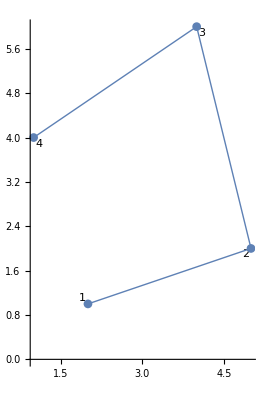

KE = (0.407005 | 0.104972 | -0.300742 | -0.139621 | -0.0902343 | -0.115496 | -0.0160288 | 0.150145
0.104972 | 0.545515 | -0.0729543 | -0.0286192 | -0.115496 | -0.277013 | 0.0834783 | -0.239883
-0.300742 | -0.0729543 | 0.702964 | -0.142679 | 0.0518507 | 0.0812231 | -0.454073 | 0.13441
-0.139621 | -0.0286192 | -0.142679 | 0.393915 | 0.14789 | -0.182347 | 0.13441 | -0.182949
-0.0902343 | -0.115496 | 0.0518507 | 0.14789 | 0.316499 | 0.107979 | -0.278116 | -0.140373
-0.115496 | -0.277013 | 0.0812231 | -0.182347 | 0.107979 | 0.4688 | -0.073706 | -0.00944048
-0.0160288 | 0.0834783 | -0.454073 | 0.13441 | -0.278116 | -0.073706 | 0.748217 | -0.144182
0.150145 | -0.239883 | 0.13441 | -0.182949 | -0.140373 | -0.00944048 | -0.144182 | 0.432273)

FE = (0.
0
0.
0
0.
0
0.
0)

```mathematica
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{5,2},{4,6},{1,4}}};
topol={{1,2,3,4}};
nnodes=Flatten[allcoords,1]
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
{KE,FE}=Assemble[allcoords,topol,1,1];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
```

{{2,1},{3.5,1.5},{5,2},{4.5,4},{4,6},{2.5,5},{1,4},{1.5,2.5},{3,3}}

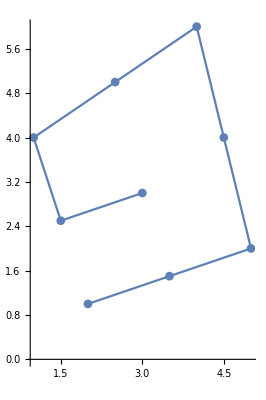

KE = (0.464716 | -0.379787 | 0.633295 | -0.110761 | 0.000416633 | -0.011653 | 0.178568 | -0.0747312 | 0.0827063 | 0.0523134 | -0.0498831 | 0.0031279 | -0.0492914 | 0.0191174 | -1.73766 | 0.623235 | 0.47713 | -0.120861
-0.379787 | 0.992705 | -0.132983 | 0.261928 | -0.011653 | -0.040121 | -0.052509 | -0.0430957 | 0.141202 | -0.0912283 | 0.0031279 | 0.0658811 | 0.0191174 | -0.105572 | 0.534346 | -1.34643 | -0.120861 | 0.305937
0.633295 | -0.132983 | -2.18809 | 0.260586 | 0.115864 | 0.0901629 | 0.0298056 | 0.00398036 | -0.4739 | 0.10328 | 0.283368 | -0.177068 | -0.52023 | 0.0281782 | -0.0914241 | -0.00997988 | 2.21131 | -0.166157
-0.110761 | 0.261928 | 0.260586 | -1.30423 | 0.0679407 | 0.112252 | 0.00398036 | 0.015393 | 0.0143915 | -0.0405346 | -0.088179 | 0.285037 | 0.0281782 | -0.213697 | -0.00997988 | -0.059185 | -0.166157 | 0.943039
0.000416633 | -0.011653 | 0.115864 | 0.0679407 | 0.436454 | 0.454572 | -0.27249 | -0.0908237 | 0.226917 | 0.147905 | -0.109675 | -0.162347 | 0.925103 | 0.245843 | 0.0725284 | 0.059504 | -1.39512 | -0.710941
-0.011653 | -0.040121 | 0.0901629 | 0.112252 | 0.454572 | 1.51565 | -0.113046 | -0.460515 | 0.147905 | 0.70359 | -0.251236 | -0.185432 | 0.334732 | 1.67459 | 0.059504 | 0.211495 | -0.710941 | -3.53151
0.178568 | -0.052509 | 0.0298056 | 0.00398036 | -0.27249 | -0.113046 | -0.120735 | -0.0887096 | -0.0230882 | -0.0763824 | -0.00573208 | -0.0336819 | -0.00572597 | -0.0356301 | -0.00641912 | 0.02693 | 0.225817 | 0.369048
-0.0747312 | -0.0430957 | 0.00398036 | 0.015393 | -0.0908237 | -0.460515 | -0.0887096 | 0.0360673 | -0.0763824 | -0.20436 | -0.0336819 | 0.0177729 | -0.124519 | -0.661834 | 0.115819 | 0.418412 | 0.369048 | 0.882159
0.0827063 | 0.141202 | -0.4739 | 0.0143915 | 0.226917 | 0.147905 | -0.0230882 | -0.0763824 | -0.359425 | 0.184734 | 0.132229 | -0.011745 | -0.0652791 | 0.179441 | -0.367327 | 0.185969 | 0.847166 | -0.765515
0.0523134 | -0.0912283 | 0.10328 | -0.0405346 | 0.147905 | 0.70359 | -0.0763824 | -0.20436 | 0.184734 | -0.197555 | -0.011745 | -0.116556 | 0.179441 | 0.434079 | 0.185969 | 0.0205552 | -0.765515 | -0.507991
-0.0498831 | 0.0031279 | 0.283368 | -0.088179 | -0.109675 | -0.251236 | -0.00573208 | -0.0336819 | 0.132229 | -0.011745 | -0.382666 | -0.166704 | 0.100317 | 0.0426589 | -0.179339 | -0.142615 | 0.211381 | 0.648374
0.0031279 | 0.0658811 | -0.177068 | 0.285037 | -0.162347 | -0.185432 | -0.0336819 | 0.0177729 | -0.011745 | -0.116556 | -0.166704 | -0.250148 | 0.0426589 | 0.00516958 | -0.142615 | -0.268481 | 0.648374 | 0.446756
-0.0492914 | 0.0191174 | -0.52023 | 0.0281782 | 0.925103 | 0.334732 | -0.00572597 | -0.124519 | -0.0652791 | 0.179441 | 0.100317 | 0.0426589 | 0.126889 | 0.263488 | -0.107097 | -0.0163606 | -0.404686 | -0.726737
0.0191174 | -0.105572 | 0.0281782 | -0.213697 | 0.245843 | 1.67459 | -0.0356301 | -0.661834 | 0.179441 | 0.434079 | 0.0426589 | 0.00516958 | 0.263488 | 0.95929 | -0.0163606 | 0.223156 | -0.726737 | -2.31518
-1.73766 | 0.534346 | -0.0914241 | -0.00997988 | 0.0725284 | 0.059504 | -0.00641912 | 0.115819 | -0.367327 | 0.185969 | -0.179339 | -0.142615 | -0.107097 | -0.0163606 | 2.59816 | -0.415512 | -0.181427 | -0.31117
0.623235 | -1.34643 | -0.00997988 | -0.059185 | 0.059504 | 0.211495 | 0.02693 | 0.418412 | 0.185969 | 0.0205552 | -0.142615 | -0.268481 | -0.0163606 | 0.223156 | -0.415512 | 1.91729 | -0.31117 | -1.11681
0.47713 | -0.120861 | 2.21131 | -0.166157 | -1.39512 | -0.710941 | 0.225817 | 0.369048 | 0.847166 | -0.765515 | 0.211381 | 0.648374 | -0.404686 | -0.726737 | -0.181427 | -0.31117 | -1.99157 | 1.78396
-0.120861 | 0.305937 | -0.166157 | 0.943039 | -0.710941 | -3.53151 | 0.369048 | 0.882159 | -0.765515 | -0.507991 | 0.648374 | 0.446756 | -0.726737 | -2.31518 | -0.31117 | -1.11681 | 1.78396 | 4.8936)

FE = (0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0)

```mathematica
order=2;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{3.5,1.5},{5,2},{4.5,4},{4,6},{2.5,5},{1,4},{1.5,2.5},{3,3}}};
topol={{1,2,3,4,5,6,7,8,9}};
nnodes=Flatten[allcoords,1]
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
```

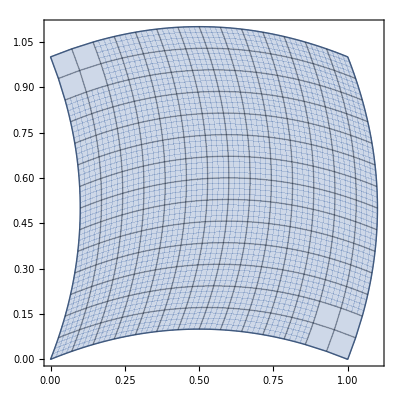

```mathematica
Clear[xi,eta,psis];
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
co={{0,0},{1,0},{1,1},{0,1},{0.5,0.1},{1.1,0.5},{0.5,1.1},{0.1,0.5},{0.6,0.6}};
{x,y}=Sum[co[[i]] psis[[i]],{i,1,Length[psis]}];
ParametricPlot[{x,y},{xi,-1,1},{eta,-1,1},Mesh->Full]
```

```mathematica
order=2;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{1,0},{1,1},{0,1},{0.5,0.1},{1.1,0.5},{0.5,1.1},{0.1,0.5},{0.6,0.6}}};
nnodes=Flatten[allcoords,1];
topol={{1,2,3,4,5,6,7,8,9}};
forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
```

KE = (0.304372 | 0.063361 | -0.00165348 | 0.00547731 | -0.0176942 | -0.0186171 | -0.0692012 | -0.0167449 | -0.30393 | -0.0176757 | 0.044873 | 0.0676615 | 0.0596972 | 0.0676615 | 0.00936971 | 0.0712132 | -0.0258332 | -0.222337
0.063361 | 0.304372 | -0.0167449 | -0.0692012 | -0.0186171 | -0.0176942 | 0.00547731 | -0.00165348 | 0.0712132 | 0.00936971 | 0.0676615 | 0.0596972 | 0.0676615 | 0.044873 | -0.0176757 | -0.30393 | -0.222337 | -0.0258332
-0.00165348 | -0.0167449 | 0.382814 | -0.140771 | -0.0555249 | 0.0220751 | -0.0176942 | 0.0191116 | -0.283581 | 0.147535 | -0.0267964 | -0.155421 | 0.0583536 | -0.0686504 | 0.089964 | -0.0823288 | -0.145881 | 0.275195
0.00547731 | -0.0692012 | -0.140771 | 0.561382 | -0.000147113 | 0.0284094 | 0.0191116 | -0.0176942 | 0.0586463 | -0.00596161 | -0.0665326 | -0.329621 | -0.0686504 | 0.0441508 | -0.0823288 | 0.158849 | 0.275195 | -0.370313
-0.0176942 | -0.0186171 | -0.0555249 | -0.000147113 | 0.780839 | 0.334214 | 0.0284094 | 0.0220751 | 0.157505 | 0.0813399 | -0.0245005 | 0.00424122 | -0.378141 | -0.0846477 | 0.0892418 | 0.0813399 | -0.580134 | -0.419798
-0.0186171 | -0.0176942 | 0.0220751 | 0.0284094 | 0.334214 | 0.780839 | -0.000147113 | -0.0555249 | 0.0813399 | 0.0892418 | -0.0846477 | -0.378141 | 0.00424122 | -0.0245005 | 0.0813399 | 0.157505 | -0.419798 | -0.580134
-0.0692012 | 0.00547731 | -0.0176942 | 0.0191116 | 0.0284094 | -0.000147113 | 0.561382 | -0.140771 | 0.158849 | -0.0823288 | 0.0441508 | -0.0686504 | -0.329621 | -0.0665326 | -0.00596161 | 0.0586463 | -0.370313 | 0.275195
-0.0167449 | -0.00165348 | 0.0191116 | -0.0176942 | 0.0220751 | -0.0555249 | -0.140771 | 0.382814 | -0.0823288 | 0.089964 | -0.0686504 | 0.0583536 | -0.155421 | -0.0267964 | 0.147535 | -0.283581 | 0.275195 | -0.145881
-0.30393 | 0.0712132 | -0.283581 | 0.0586463 | 0.157505 | 0.0813399 | 0.158849 | -0.0823288 | 1.56213 | -0.190181 | -0.36907 | -0.274454 | -0.119967 | -0.00384681 | -0.584266 | 0.423013 | -0.217669 | -0.0834013
-0.0176757 | 0.00936971 | 0.147535 | -0.00596161 | 0.0813399 | 0.0892418 | -0.0823288 | 0.089964 | -0.190181 | 1.8153 | -0.274454 | -0.147124 | -0.00384681 | 0.107525 | 0.423013 | -0.584266 | -0.0834013 | -1.37405
0.044873 | 0.0676615 | -0.0267964 | -0.0665326 | -0.0245005 | -0.0846477 | 0.0441508 | -0.0686504 | -0.36907 | -0.274454 | 1.59946 | 0.10613 | -0.0217015 | 0.225551 | 0.107525 | -0.00384681 | -1.35394 | 0.0987885
0.0676615 | 0.0596972 | -0.155421 | -0.329621 | 0.00424122 | -0.378141 | -0.0686504 | 0.0583536 | -0.274454 | -0.147124 | 0.10613 | 1.08747 | 0.225551 | -0.0217015 | -0.00384681 | -0.119967 | 0.0987885 | -0.208967
0.0596972 | 0.0676615 | 0.0583536 | -0.0686504 | -0.378141 | 0.00424122 | -0.329621 | -0.155421 | -0.119967 | -0.00384681 | -0.0217015 | 0.225551 | 1.08747 | 0.10613 | -0.147124 | -0.274454 | -0.208967 | 0.0987885
0.0676615 | 0.044873 | -0.0686504 | 0.0441508 | -0.0846477 | -0.0245005 | -0.0665326 | -0.0267964 | -0.00384681 | 0.107525 | 0.225551 | -0.0217015 | 0.10613 | 1.59946 | -0.274454 | -0.36907 | 0.0987885 | -1.35394
0.00936971 | -0.0176757 | 0.089964 | -0.0823288 | 0.0892418 | 0.0813399 | -0.00596161 | 0.147535 | -0.584266 | 0.423013 | 0.107525 | -0.00384681 | -0.147124 | -0.274454 | 1.8153 | -0.190181 | -1.37405 | -0.0834013
0.0712132 | -0.30393 | -0.0823288 | 0.158849 | 0.0813399 | 0.157505 | 0.0586463 | -0.283581 | 0.423013 | -0.584266 | -0.00384681 | -0.119967 | -0.274454 | -0.36907 | -0.190181 | 1.56213 | -0.0834013 | -0.217669
-0.0258332 | -0.222337 | -0.145881 | 0.275195 | -0.580134 | -0.419798 | -0.370313 | 0.275195 | -0.217669 | -0.0834013 | -1.35394 | 0.0987885 | -0.208967 | 0.0987885 | -1.37405 | -0.0834013 | 4.27679 | 0.06097
-0.222337 | -0.0258332 | 0.275195 | -0.370313 | -0.419798 | -0.580134 | 0.275195 | -0.145881 | -0.0834013 | -1.37405 | 0.0987885 | -0.208967 | 0.0987885 | -1.35394 | -0.0834013 | -0.217669 | 0.06097 | 4.27679)

FE = (0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0)

{{4,3,2,1,4},{2,1,4,3,2},{2,1,4,3,2},{3,4,1,2,3},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4}}

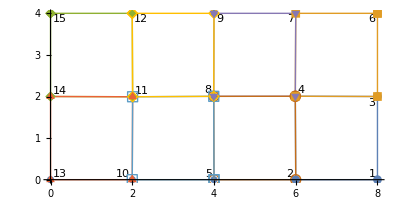

co = {{6,4},{8,4}}

co = {{0,4},{2,4}}

co = {{4,4},{6,4}}

co = {{2,4},{4,4}}

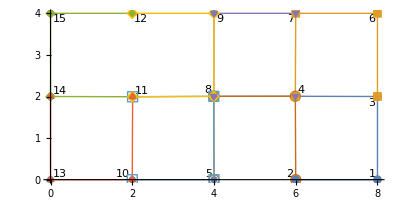

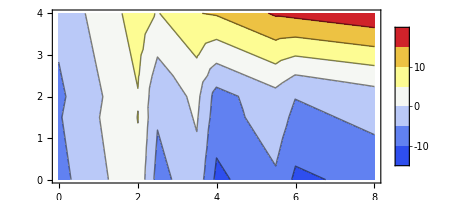

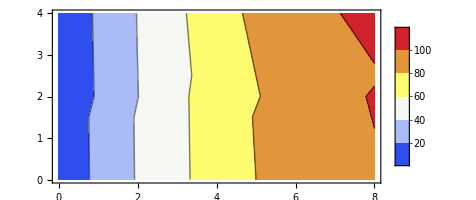

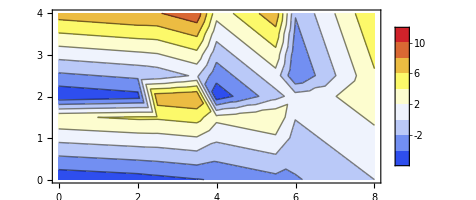

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidels-ex1-p1.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidnodes-ex1-p1.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListLinePlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=MapThread[Part[#1,#2]&,{allcoords,ord}];
(*or*)
allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,13,1,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,6,{{10^12,1},{1,1}},{0,0}];

q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=-ContributeLineNewman[FE,f,order,nnodes,topol,15,6,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Banded"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]




defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All];

{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[(dsols),30 10^6,0.30][[1]];
stresslists={};
sx=1;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]


stresslists={};
sx=2;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]

stresslists={};
sx=3;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]
```

{{0,0},{10,0},{10,10},{0,10}}

{{2,1,4,3,2}}

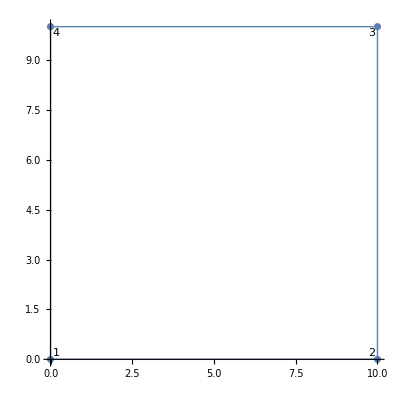

{{2,1,4,3,2}}

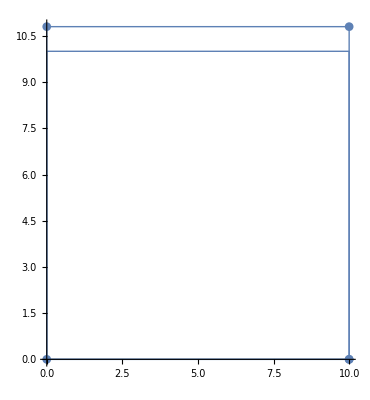

{0,0,0,0,0,0,0,0}

```mathematica
order=1;
young=30 10^6;
nu=0.;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol={{1,2,3,4}};
nnodes={{0,0},{10,0},{10,10},{0,10}}
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];



undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,2,{{10^12,1},{1,10^12}},{0,0}];


{KE,FE}=ApplyNodeBC[KE,FE,4,1,{{1,1},{1,1}},{0,150}];
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{0,150}];

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=80000;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick},PlotMarkers->Automatic];

Show[defplot,undefplot,PlotRange->All]

KE.sol-FE//Chop
```

```mathematica
allcoordsNEW
```

{{{10.,8.×10^-13},{0.,8.×10^-13},{0.,10.8},{10.,10.8},{10.,8.×10^-13}}}

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{4,7,3,6,2,5,1,8,4}}

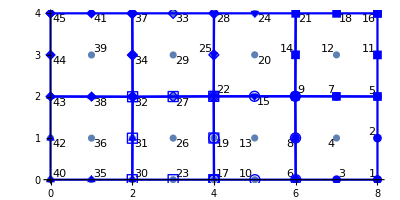

co = {{6,4},{7,4},{8,4}}

co = {{0,4},{1,4},{2,4}}

co = {{4,4},{5,4},{6,4}}

co = {{2,4},{3,4},{4,4}}

{{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{1,5,2,6,3,7,4,8,1},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5}}

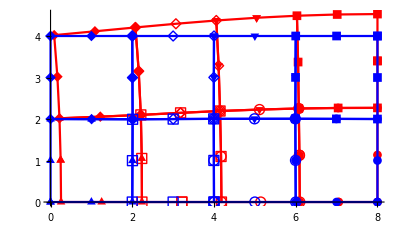

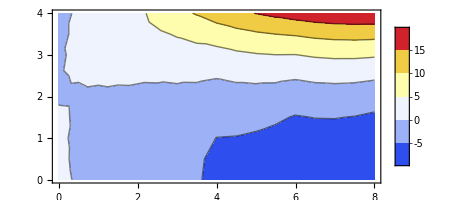

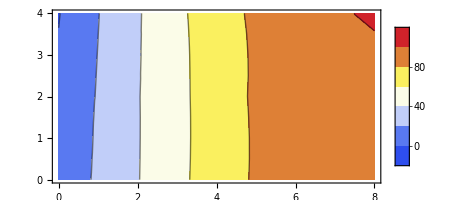

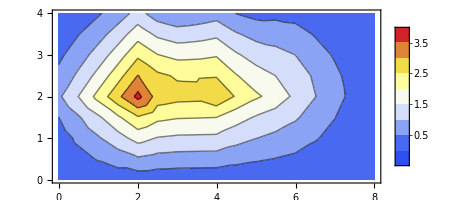

```mathematica
order=2;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp2els9nodes.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp2nodes9nodes.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,9}];

allcoords2=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords2]&@Flatten[nf@Flatten[allcoords2,1],1];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords2//Flatten[#,1]&

allcoordsNEW=Table[allcoords2[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],PlotMarkers->Automatic,AspectRatio->Automatic,PlotStyle->{Blue}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,40,1,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,16,{{10^12,1},{1,1}},{0,0}];

fE=FE;

(*{KE,FE}=ApplyNodeBC[KE,FE,16,1,{{1,1},{1,1}},{0,33.53}];
{KE,FE}=ApplyNodeBC[KE,FE,18,1,{{1,1},{1,1}},{0,130.26}];
{KE,FE}=ApplyNodeBC[KE,FE,21,1,{{1,1},{1,1}},{0,62.06}];
{KE,FE}=ApplyNodeBC[KE,FE,24,1,{{1,1},{1,1}},{0,110.43}];
{KE,FE}=ApplyNodeBC[KE,FE,28,1,{{1,1},{1,1}},{0,47.49}];
{KE,FE}=ApplyNodeBC[KE,FE,33,1,{{1,1},{1,1}},{0,73.79}];
{KE,FE}=ApplyNodeBC[KE,FE,37,1,{{1,1},{1,1}},{0,25.7}];
{KE,FE}=ApplyNodeBC[KE,FE,41,1,{{1,1},{1,1}},{0,25.9}];
{KE,FE}=ApplyNodeBC[KE,FE,45,1,{{1,1},{1,1}},{0,0.033}];*)

q=100;
L=16;
f[x_]:=q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,order,nnodes,topol,45,16,1];


sol=LinearSolve[KE,FE,Method->"Banded"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords2]&@Flatten[nf@Flatten[allcoords2,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],PlotMarkers->Automatic,AspectRatio->Automatic,PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]

{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[(dsols),30 10^6,0.30][[1]];
stresslists={};
sx=1;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]


stresslists={};
sx=2;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]

stresslists={};
sx=3;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]
```

{{0,0},{10,0},{10,10},{0,10}}

{{2,1,4,3,2}}

-Graphics-

co = {{0,10},{10,10}}

(0
0
0
0
0.
33333.3
0.
16666.7)

{{4,3,2,1,4}}

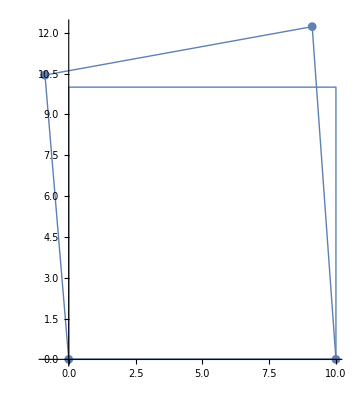

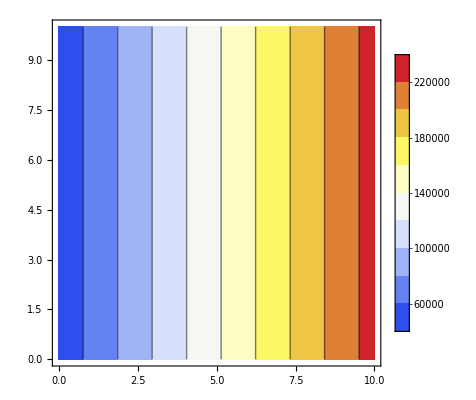

{0,0,0,0,0,0,0,0}

{-2.73379×10^-32,1.11111×10^-15,1.64027×10^-31,2.22222×10^-15,-0.00111111,0.00277778,-0.00111111,0.000555556}

```mathematica
order=1;
young=30 10^6;
nu=0.;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol={{1,2,3,4}};
nnodes={{0,0},{10,0},{10,10},{0,10}}
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];



undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,2,{{10^12,1},{1,10^12}},{0,0}];

f[x_]:=1000 x ;
diry=1;
FE=ContributeLineNewman[FE,f,order,nnodes,topol,4,3,1];

FE//MatrixForm

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=800;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick},PlotMarkers->Automatic];

Show[defplot,undefplot,PlotRange->All]


{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[(dsols),30 10^6,0.30][[1]];
stresslists={};
sx=2;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->3]

KE.sol-FE//Chop
sol
```

{{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2}}

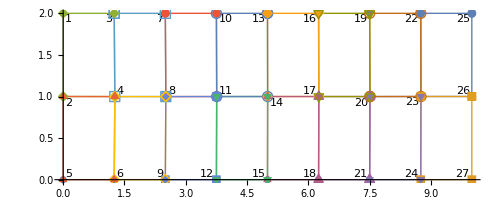

{{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2}}

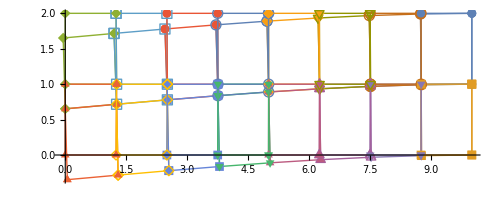

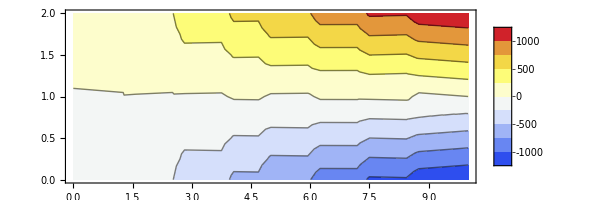

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
order=1;
young=30 10^6;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp1els.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp1nodes.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=MapThread[Part[#1,#2]&,{allcoords,ord}];
(*or*)
allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,27,25,{{10^12,1},{1,10^12}},{0,0}];


{KE,FE}=ApplyNodeBC[KE,FE,1,1,{{1,1},{1,1}},{0,-100}];
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{0,-100}];
{KE,FE}=ApplyNodeBC[KE,FE,5,1,{{1,1},{1,1}},{0,-100}];

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=80;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[defplot,undefplot,PlotRange->All]


{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[(dsols),30 10^6,0.30][[1]];
stresslists={};
sx=1;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->3]

KE.sol-FE//Chop
```

```mathematica
topol
```

{{26,25,22,23},{27,26,23,24},{1,2,4,3},{2,5,6,4},{21,24,23,20},{19,20,23,22},{7,3,4,8},{4,6,9,8},{18,21,20,17},{20,19,16,17},{10,7,8,11},{8,9,12,11},{16,13,14,17},{18,17,14,15},{12,15,14,11},{14,13,10,11}}

```mathematica
nnodes
```

{{0,2},{0,1},{1.25,2},{1.26322,0.999226},{0,0},{1.25,0},{2.5,2},{2.51167,0.999009},{2.5,0},{3.75,2},{3.75658,0.999403},{3.75,0},{5,2},{5.00304,0.999726},{5,0},{6.25,2},{6.25556,0.999501},{6.25,0},{7.5,2},{7.50756,0.999402},{7.5,0},{8.75,2},{8.75501,1.00001},{8.75,0},{10,2},{10,1},{10,0}}

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3}}

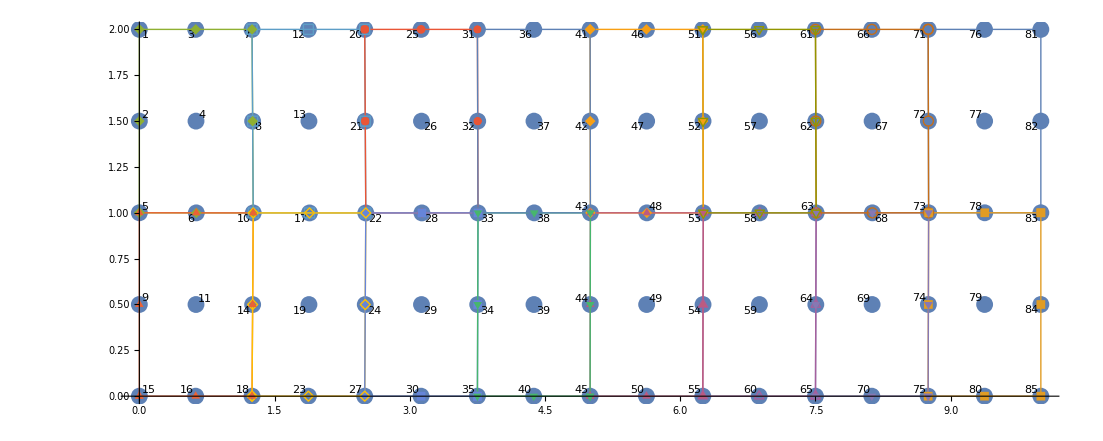

{{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{1,5,2,6,3,7,4,8,1},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{1,5,2,6,3,7,4,8,1},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5}}

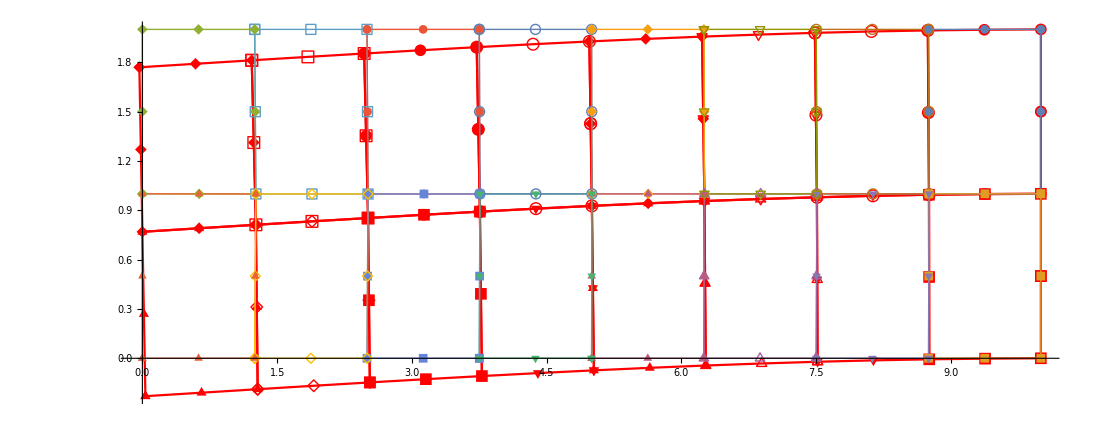

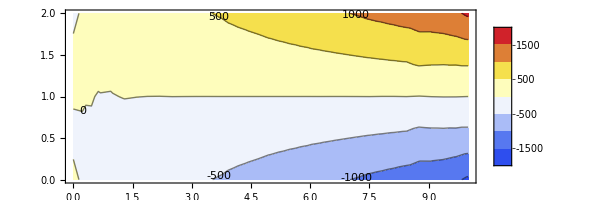

```mathematica
order=2;
young=30 10^6;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\elsp2-9-beam-redy.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\nodesp2-9-beam-redy.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,9}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

allcoords2=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords2//Flatten[#,1]&

allcoordsNEW=Table[allcoords2[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,85,81,{{10^12,1},{1,10^12}},{0,0}];


{KE,FE}=ApplyNodeBC[KE,FE,5,1,{{1,1},{1,1}},{0,-300}];

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=45;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords2]&@Flatten[nf@Flatten[allcoords2,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]


{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[(dsols),30 10^6,0.30][[1]];
stresslists={};
sx=1;
refine=0.5;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->3,ContourLabels->All]
```

```mathematica
Flatten[stresslists,2]
```

{{10.,1.,0.00121411},{9.68875,1.,6.52595},{9.3775,1.00001,7.49513},{9.06626,1.00001,2.90875},{8.75501,1.00001,-7.23317},{10.,1.25,324.255},{9.68844,1.25,323.216},{9.37688,1.25,326.63},{9.06532,1.25001,334.496},{8.75376,1.25001,346.813},{10.,1.5,694.},{9.68813,1.5,666.789},{9.37625,1.5,654.038},{9.06438,1.5,655.746},{8.7525,1.50001,671.914},{10.,1.75,1109.24},{9.68781,1.75,1037.24},{9.37563,1.75,989.718},{9.06344,1.75,966.66},{8.75125,1.75,968.068},{10.,2.,1569.97},{9.6875,2.,1434.58},{9.375,2.,1333.67},{9.0625,2.,1267.24},{8.75,2.,1235.28},{10.,0.,-1569.97},{9.6875,0.,-1434.59},{9.375,0.,-1333.69},{9.0625,0.,-1267.26},{8.75,0.,-1235.3},{10.,0.25,-1109.24},{9.68781,0.250001,-1037.25},{9.37563,0.250001,-989.725},{9.06344,0.250002,-966.668},{8.75125,0.250003,-968.079},{10.,0.5,-694.},{9.68813,0.500001,-666.789},{9.37625,0.500003,-654.037},{9.06438,0.500004,-655.745},{8.7525,0.500005,-671.912},{10.,0.75,-324.254},{9.68844,0.750002,-323.213},{9.37688,0.750004,-326.623},{9.06532,0.750006,-334.487},{8.75376,0.750008,-346.802},{10.,1.,0.00121411},{9.68875,1.,-6.51873},{9.3775,1.00001,-7.48344},{9.06626,1.00001,-2.89293},{8.75501,1.00001,7.2528},{0.,2.,-23.3045},{0.3125,2.,28.0012},{0.625,2.,73.0001},{0.9375,2.,111.692},{1.25,2.,144.077},{0.,1.75,0.646611},{0.313326,1.74995,32.5383},{0.626653,1.7499,65.8561},{0.939979,1.74985,100.6},{1.25331,1.74981,136.77},{0.,1.5,25.0428},{0.314153,1.4999,32.9126},{0.628305,1.49981,49.9414},{0.942458,1.49971,76.1291},{1.25661,1.49961,111.476},{0.,1.25,49.8842},{0.314979,1.24985,29.1241},{0.629958,1.24971,25.2559},{0.944937,1.24956,38.2796},{1.25992,1.24942,68.1952},{0.,1.,75.1706},{0.315805,0.999806,21.1727},{0.631611,0.999613,-8.20037},{0.947416,0.999419,-12.9486},{1.26322,0.999226,6.92802},{0.,1.,-75.1651},{0.315805,0.999806,-21.2664},{0.631611,0.999613,8.04093},{0.947416,0.999419,12.757},{1.26322,0.999226,-7.11814},{0.,0.75,-49.8301},{0.314979,0.749855,-29.1489},{0.629958,0.74971,-25.3271},{0.944937,0.749564,-38.3647},{1.25992,0.749419,-68.2618},{0.,0.5,-24.9765},{0.314153,0.499903,-32.8982},{0.628305,0.499806,-49.9474},{0.942458,0.49971,-76.1242},{1.25661,0.499613,-111.429},{0.,0.25,-0.604352},{0.313326,0.249952,-32.5143},{0.626653,0.249903,-65.82},{0.939979,0.249855,-100.521},{1.25331,0.249806,-136.619},{0.,0.,23.2864},{0.3125,0.,-27.9973},{0.625,0.,-72.9449},{0.9375,0.,-111.556},{1.25,0.,-143.832},{7.5,0.,-1078.77},{7.50189,0.24985,-807.411},{7.50378,0.499701,-537.063},{7.50567,0.749551,-267.724},{7.50756,0.999402,0.605649},{7.8125,0.,-1118.69},{7.81423,0.249889,-837.599},{7.81596,0.499777,-557.775},{7.81769,0.749666,-279.22},{7.81942,0.999554,-1.93287},{8.125,0.,-1161.97},{8.12657,0.249927,-869.602},{8.12814,0.499853,-578.763},{8.12971,0.74978,-289.451},{8.13128,0.999706,-1.66755},{8.4375,0.,-1208.6},{8.43891,0.249965,-903.422},{8.44032,0.499929,-600.027},{8.44173,0.749894,-298.419},{8.44315,0.999859,1.4016},{8.75,0.,-1258.6},{8.75125,0.250003,-939.058},{8.7525,0.500005,-621.568},{8.75376,0.750008,-306.123},{8.75501,1.00001,7.27459},{7.5,2.,1080.05},{7.8125,2.,1119.68},{8.125,2.,1162.65},{8.4375,2.,1208.94},{8.75,2.,1258.57},{7.50189,1.74985,808.047},{7.81423,1.74989,838.104},{8.12657,1.74993,869.955},{8.43891,1.74996,903.6},{8.75125,1.75,939.038},{7.50378,1.4997,537.045},{7.81596,1.49978,557.786},{8.12814,1.49985,578.783},{8.44032,1.49993,600.037},{8.7525,1.50001,621.547},{7.50567,1.24955,267.042},{7.81769,1.24967,278.726},{8.12971,1.24978,289.13},{8.44173,1.24989,298.253},{8.75376,1.25001,306.095},{7.50756,0.999402,-1.96197},{7.81942,0.999554,0.926293},{8.13128,0.999706,0.996443},{8.44315,0.999859,-1.75153},{8.75501,1.00001,-7.31762},{2.5,2.,347.037},{2.50292,1.74975,265.896},{2.50583,1.4995,181.068},{2.50875,1.24926,92.5526},{2.51167,0.999009,0.350623},{2.1875,2.,309.942},{2.19051,1.74977,234.221},{2.19353,1.49953,157.108},{2.19654,1.2493,78.604},{2.19955,0.999063,-1.29144},{1.875,2.,271.105},{1.87811,1.74978,201.799},{1.88122,1.49956,133.398},{1.88433,1.24934,65.9016},{1.88744,0.999117,-0.690639},{1.5625,2.,230.523},{1.56571,1.74979,168.63},{1.56892,1.49959,109.938},{1.57212,1.24938,54.4454},{1.57533,0.999171,2.15301},{1.25,2.,188.198},{1.25331,1.74981,134.715},{1.25661,1.49961,86.7271},{1.25992,1.24942,44.2355},{1.26322,0.999226,7.23951},{1.26322,0.999226,-7.48338},{1.57533,0.999171,-2.51902},{1.88744,0.999117,0.210411},{2.19955,0.999063,0.704903},{2.51167,0.999009,-1.03554},{1.25992,0.749419,-44.3585},{1.57212,0.749379,-54.6337},{1.88433,0.749338,-66.1476},{2.19654,0.749297,-78.9001},{2.50875,0.749257,-92.8914},{1.25661,0.499613,-86.7228},{1.56892,0.499586,-109.943},{1.88122,0.499559,-133.406},{2.19353,0.499532,-157.111},{2.50583,0.499505,-181.059},{1.25331,0.249806,-134.576},{1.56571,0.249793,-168.448},{1.87811,0.249779,-201.565},{2.19051,0.249766,-233.929},{2.50292,0.249752,-265.539},{1.25,0.,-187.919},{1.5625,0.,-230.147},{1.875,0.,-270.625},{2.1875,0.,-309.353},{2.5,0.,-346.331},{6.25,0.,-899.649},{6.25139,0.249875,-672.459},{6.25278,0.49975,-446.833},{6.25417,0.749626,-222.771},{6.25556,0.999501,-0.271489},{6.5625,0.,-940.579},{6.56401,0.249869,-704.679},{6.56553,0.499738,-469.394},{6.56704,0.749607,-234.726},{6.56856,0.999476,-0.673606},{6.875,0.,-981.954},{6.87664,0.249863,-737.127},{6.87828,0.499726,-491.969},{6.87992,0.749588,-246.479},{6.88156,0.999451,-0.657846},{7.1875,0.,-1023.77},{7.18926,0.249857,-769.805},{7.19103,0.499713,-514.556},{7.19279,0.74957,-258.03},{7.19456,0.999427,-0.224213},{7.5,0.,-1066.04},{7.50189,0.24985,-802.711},{7.50378,0.499701,-537.158},{7.50567,0.749551,-269.378},{7.50756,0.999402,0.627292},{7.50756,0.999402,-1.90875},{7.19456,0.999427,-0.960084},{6.88156,0.999451,-0.426424},{6.56856,0.999476,-0.307774},{6.25556,0.999501,-0.604137},{7.50567,1.24955,268.741},{7.19279,1.24957,257.438},{6.87992,1.24959,245.935},{6.56704,1.24961,234.233},{6.25417,1.24963,222.332},{7.50378,1.4997,537.163},{7.19103,1.49971,514.556},{6.87828,1.49973,491.965},{6.56553,1.49974,469.392},{6.25278,1.49975,446.835},{7.50189,1.74985,803.357},{7.18926,1.74986,770.395},{6.87664,1.74986,737.665},{6.56401,1.74987,705.169},{6.25139,1.74988,672.905},{7.5,2.,1067.32},{7.1875,2.,1024.95},{6.875,2.,983.034},{6.5625,2.,941.563},{6.25,2.,900.541},{3.75,2.,529.897},{3.75165,1.74985,399.885},{3.75329,1.4997,268.189},{3.75494,1.24955,134.809},{3.75658,0.999403,-0.25644},{3.4375,2.,488.715},{3.43946,1.74983,367.592},{3.44143,1.49965,245.686},{3.44339,1.24948,122.995},{3.44535,0.999304,-0.48032},{3.125,2.,447.282},{3.12728,1.7498,335.173},{3.12956,1.4996,223.181},{3.13184,1.2494,111.304},{3.13412,0.999206,-0.456147},{2.8125,2.,405.599},{2.8151,1.74978,302.629},{2.8177,1.49955,200.675},{2.8203,1.24933,99.7373},{2.8229,0.999108,-0.183917},{2.5,2.,363.665},{2.50292,1.74975,269.958},{2.50583,1.4995,178.168},{2.50875,1.24926,88.2937},{2.51167,0.999009,0.336369},{2.51167,0.999009,-1.09272},{2.8229,0.999108,-0.541261},{3.13412,0.999206,-0.248358},{3.44535,0.999304,-0.214008},{3.75658,0.999403,-0.43821},{2.50875,0.749257,-88.6763},{2.8203,0.749331,-100.094},{3.13184,0.749404,-111.646},{3.44339,0.749478,-123.334},{3.75494,0.749552,-135.158},{2.50583,0.499505,-178.182},{2.8177,0.499554,-200.668},{3.12956,0.499603,-223.167},{3.44143,0.499652,-245.678},{3.75329,0.499701,-268.201},{2.50292,0.249752,-269.609},{2.8151,0.249777,-302.265},{3.12728,0.249801,-334.811},{3.43946,0.249826,-367.245},{3.75165,0.249851,-399.568},{2.5,0.,-362.958},{2.8125,0.,-404.885},{3.125,0.,-446.577},{3.4375,0.,-488.035},{3.75,0.,-529.259},{6.25,2.,887.733},{6.25139,1.74988,668.836},{6.25278,1.49975,447.816},{6.25417,1.24963,224.672},{6.25556,0.999501,-0.595593},{5.9375,2.,845.984},{5.93873,1.74989,636.191},{5.93996,1.49978,425.19},{5.94119,1.24967,212.98},{5.94243,0.999557,-0.438078},{5.625,2.,804.307},{5.62607,1.7499,603.591},{5.62715,1.49981,402.582},{5.62822,1.24971,201.279},{5.6293,0.999613,-0.317134},{5.3125,2.,762.703},{5.31342,1.74992,571.036},{5.31433,1.49983,379.991},{5.31525,1.24975,189.568},{5.31617,0.99967,-0.232763},{5.,2.,721.171},{5.00076,1.74993,538.527},{5.00152,1.49986,357.419},{5.00228,1.24979,177.848},{5.00304,0.999726,-0.184972},{6.25,0.,-886.844},{5.9375,0.,-845.232},{5.625,0.,-803.683},{5.3125,0.,-762.197},{5.,0.,-720.775},{6.25139,0.249875,-668.389},{5.93873,0.249889,-635.818},{5.62607,0.249903,-603.284},{5.31342,0.249917,-570.787},{5.00076,0.249931,-538.327},{6.25278,0.49975,-447.808},{5.93996,0.499779,-425.194},{5.62715,0.499807,-402.589},{5.31433,0.499835,-379.995},{5.00152,0.499863,-357.411},{6.25417,0.749626,-225.101},{5.94119,0.749668,-213.358},{5.62822,0.74971,-201.598},{5.31525,0.749752,-189.822},{5.00228,0.749794,-178.029},{6.25556,0.999501,-0.268199},{5.94243,0.999557,-0.310577},{5.6293,0.999613,-0.310102},{5.31617,0.99967,-0.26677},{5.00304,0.999726,-0.180576},{3.75,0.,-541.796},{3.75165,0.249851,-403.722},{3.75329,0.499701,-267.47},{3.75494,0.749552,-133.041},{3.75658,0.999403,-0.434283},{4.0625,0.,-583.452},{4.06392,0.249871,-436.202},{4.06535,0.499742,-289.93},{4.06677,0.749613,-144.635},{4.0682,0.999484,-0.316745},{4.375,0.,-625.102},{4.3762,0.249891,-468.688},{4.3774,0.499782,-312.407},{4.37861,0.749673,-156.258},{4.37981,0.999564,-0.24071},{4.6875,0.,-666.746},{4.68848,0.249911,-501.18},{4.68946,0.499823,-334.902},{4.69044,0.749734,-167.91},{4.69142,0.999645,-0.206175},{5.,0.,-708.384},{5.00076,0.249931,-533.678},{5.00152,0.499863,-357.414},{5.00228,0.749794,-179.593},{5.00304,0.999726,-0.213138},{5.00304,0.999726,-0.217486},{4.69142,0.999645,-0.275123},{4.37981,0.999564,-0.299873},{4.0682,0.999484,-0.291733},{3.75658,0.999403,-0.250698},{5.00228,1.24979,179.375},{4.69044,1.24973,167.675},{4.37861,1.24967,155.995},{4.06677,1.24961,144.335},{3.75494,1.24955,132.695},{5.00152,1.49986,357.404},{4.68946,1.49982,334.907},{4.3774,1.49978,312.418},{4.06535,1.49974,289.935},{3.75329,1.4997,267.459},{5.00076,1.74993,533.869},{4.68848,1.74991,501.421},{4.3762,1.74989,468.967},{4.06392,1.74987,436.507},{3.75165,1.74985,404.041},{5.,2.,708.771},{4.6875,2.,667.217},{4.375,2.,625.644},{4.0625,2.,584.052},{3.75,2.,542.44}}

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,6,3,7,4,8,1,5,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{8,4,7,3,6,2,5,1,8},{2,6,3,7,4,8,1,5,2},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{3,6,2,5,1,8,4,7,3},{4,8,1,5,2,6,3,7,4},{5,1,8,4,7,3,6,2,5},{3,6,2,5,1,8,4,7,3},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{4,7,3,6,2,5,1,8,4},{5,1,8,4,7,3,6,2,5},{3,6,2,5,1,8,4,7,3},{5,2,6,3,7,4,8,1,5},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{2,6,3,7,4,8,1,5,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5}}

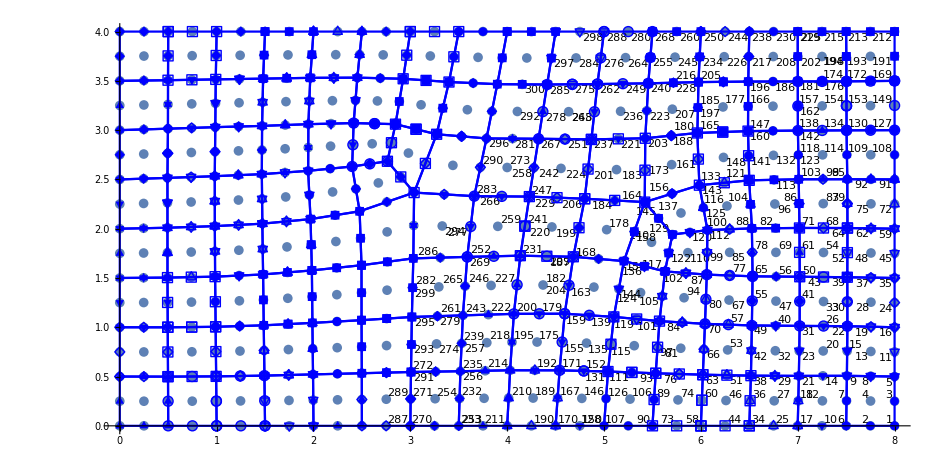

co = {{7.5,4},{7.75,4},{8,4}}

co = {{0,4},{0.25,4},{0.5,4}}

co = {{0.5,4},{0.75,4},{1,4}}

co = {{7,4},{7.25,4},{7.5,4}}

co = {{1,4},{1.25,4},{1.5,4}}

co = {{6.5,4},{6.75,4},{7,4}}

co = {{1.5,4},{1.75,4},{2,4}}

co = {{6,4},{6.25,4},{6.5,4}}

co = {{2,4},{2.25,4},{2.5,4}}

co = {{5.5,4},{5.75,4},{6,4}}

co = {{2.5,4},{2.75,4},{3,4}}

co = {{5,4},{5.25,4},{5.5,4}}

co = {{3,4},{3.25,4},{3.5,4}}

co = {{4.5,4},{4.75,4},{5,4}}

co = {{3.5,4},{3.75,4},{4,4}}

co = {{4,4},{4.25,4},{4.5,4}}

{{3,6,2,5,1,8,4,7,3},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{1,5,2,6,3,7,4,8,1},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5}}

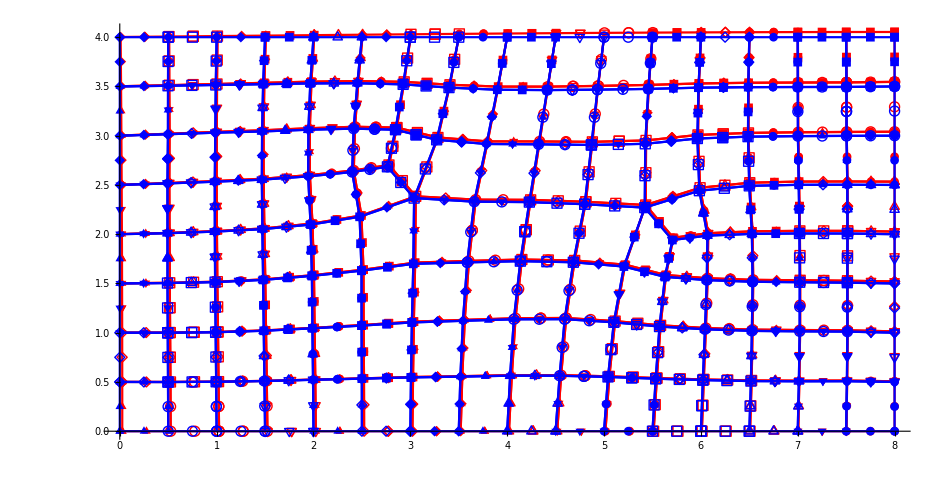

```mathematica
order=2;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\elsturbo.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\nosturbo.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,9}];

allcoords2=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords2]&@Flatten[nf@Flatten[allcoords2,1],1];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords2//Flatten[#,1]&

allcoordsNEW=Table[allcoords2[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],PlotMarkers->Automatic,AspectRatio->Automatic,PlotStyle->{Blue}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,507,1,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,212,{{10^12,1},{1,1}},{0,0}];

fE=FE;

(*{KE,FE}=ApplyNodeBC[KE,FE,16,1,{{1,1},{1,1}},{0,33.53}];
{KE,FE}=ApplyNodeBC[KE,FE,18,1,{{1,1},{1,1}},{0,130.26}];
{KE,FE}=ApplyNodeBC[KE,FE,21,1,{{1,1},{1,1}},{0,62.06}];
{KE,FE}=ApplyNodeBC[KE,FE,24,1,{{1,1},{1,1}},{0,110.43}];
{KE,FE}=ApplyNodeBC[KE,FE,28,1,{{1,1},{1,1}},{0,47.49}];
{KE,FE}=ApplyNodeBC[KE,FE,33,1,{{1,1},{1,1}},{0,73.79}];
{KE,FE}=ApplyNodeBC[KE,FE,37,1,{{1,1},{1,1}},{0,25.7}];
{KE,FE}=ApplyNodeBC[KE,FE,41,1,{{1,1},{1,1}},{0,25.9}];
{KE,FE}=ApplyNodeBC[KE,FE,45,1,{{1,1},{1,1}},{0,0.033}];*)

q=100;
L=16;
f[x_]:=q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,order,nnodes,topol,541,212,1];


sol=LinearSolve[KE,FE,Method->"Banded"];
scale=8000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords2]&@Flatten[nf@Flatten[allcoords2,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],PlotMarkers->Automatic,AspectRatio->Automatic,PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]

(*{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[(dsols),30 10^6,0.30][[1]];
stresslists={};
sx=1;
refine=0.75;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]


stresslists={};
sx=2;
refine=0.75;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]

stresslists={};
sx=3;
refine=0.75;
For[i=1,i≤Length[stress],i++,

stresslist=Table[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]*)
```

```mathematica
sol[[212 2]]
```

0.000013215

```mathematica
stresslists={};
sx=1;
refine=1;
xi=Table[xi,{xi,-1,1,refine}];
eta=Table[eta,{eta,-1,1,refine}];
xx[Xi_,Eta_]:=X[[1,1]]/.{xi->Xi,eta->Eta};
yy[Xi_,Eta_]:=X[[1,2]]/.{xi->Xi,eta->Eta};
ss[Xi_,Eta_]:=stress[[1,sx]]/.{xi->Xi,eta->Eta};
stresslist={xx[#1,#2],yy[#1,#2],ss[#1,#2]}&[xi,eta]//AbsoluteTiming
stresslist=ParallelTable[{X[[1,1]],X[[1,2]],stress[[1,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}]//AbsoluteTiming
```

{1.48117,{{7.5,7.75191,8.},{0.,0.251858,0.5},{-0.548843,-0.534195,-0.512512}}}

{2.36176,{{{7.5,0.,-0.548843},{7.50382,0.253716,-0.538989},{7.50764,0.507432,-0.516531}},{{7.75,0.,-0.543911},{7.75191,0.251858,-0.534195},{7.75382,0.503716,-0.512091}},{{8.,0.,-0.544059},{8.,0.25,-0.53437},{8.,0.5,-0.512512}}}}

```mathematica
stresslists={};
sx=1;
refine=1;
Clear[xi,eta];
xxi=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
eeta=Table[eta,{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,

xx[Xi_,Eta_]:=X[[i,1]]/.{xi->Xi,eta->Eta};
yy[Xi_,Eta_]:=X[[i,2]]/.{xi->Xi,eta->Eta};
ss[Xi_,Eta_]:=stress[[i,sx]]/.{xi->Xi,eta->Eta};
stresslist={xx[#1,#2],yy[#1,#2],ss[#1,#2]}&[xxi];
AppendTo[stresslists,stresslist];

];
lp=Flatten[stresslists,1];
ListDensityPlot[lp]
```

Function::slotn: Slot number 2 in {xx[#1,#2],yy[#1,#2],ss[#1,#2]}& cannot be filled from ({xx[#1,#2],yy[#1,#2],ss[#1,#2]}&)[{{{-1,-1},{-1,0},{-1,1}},{{0,-1},{0,0},{0,1}},{{1,-1},{1,0},{1,1}}}].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

$Aborted

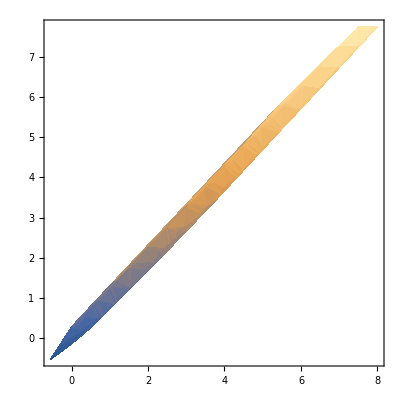

```mathematica
lp=Flatten[stresslists,1];
ListDensityPlot[lp]
```

```mathematica
xx[Xi_,Eta_]:=X[[1,1]]/.{xi->Xi,eta->Eta}
```

```mathematica
xx[0,0]
```

7.75191

```mathematica
l1=({X[[1,1]],X[[1,2]],stress[[1,sx]]}/.{xi->#})&@xieta;
l2=l1/.{eta->#}&@xieta
```

{{{{{7.5,7.5,7.5},{7.50382,7.50382,7.50382},{7.50764,7.50764,7.50764}},{{7.5,7.5,7.5},{7.50382,7.50382,7.50382},{7.50764,7.50764,7.50764}},{{7.5,7.5,7.5},{7.50382,7.50382,7.50382},{7.50764,7.50764,7.50764}}},{{{7.75,7.75,7.75},{7.75191,7.75191,7.75191},{7.75382,7.75382,7.75382}},{{7.75,7.75,7.75},{7.75191,7.75191,7.75191},{7.75382,7.75382,7.75382}},{{7.75,7.75,7.75},{7.75191,7.75191,7.75191},{7.75382,7.75382,7.75382}}},{{{8.,8.,8.},{8.,8.,8.},{8.,8.,8.}},{{8.,8.,8.},{8.,8.,8.},{8.,8.,8.}},{{8.,8.,8.},{8.,8.,8.},{8.,8.,8.}}}},{{{{0.,0.,0.},{0.253716,0.253716,0.253716},{0.507432,0.507432,0.507432}},{{0.,0.,0.},{0.253716,0.253716,0.253716},{0.507432,0.507432,0.507432}},{{0.,0.,0.},{0.253716,0.253716,0.253716},{0.507432,0.507432,0.507432}}},{{{0.,0.,0.},{0.251858,0.251858,0.251858},{0.503716,0.503716,0.503716}},{{0.,0.,0.},{0.251858,0.251858,0.251858},{0.503716,0.503716,0.503716}},{{0.,0.,0.},{0.251858,0.251858,0.251858},{0.503716,0.503716,0.503716}}},{{{0.,0.,0.},{0.25,0.25,0.25},{0.5,0.5,0.5}},{{0.,0.,0.},{0.25,0.25,0.25},{0.5,0.5,0.5}},{{0.,0.,0.},{0.25,0.25,0.25},{0.5,0.5,0.5}}}},{{{{-0.548843,-0.548843,-0.548843},{-0.538989,-0.538989,-0.538989},{-0.516531,-0.516531,-0.516531}},{{-0.548843,-0.548843,-0.548843},{-0.538989,-0.538989,-0.538989},{-0.516531,-0.516531,-0.516531}},{{-0.548843,-0.548843,-0.548843},{-0.538989,-0.538989,-0.538989},{-0.516531,-0.516531,-0.516531}}},{{{-0.543911,-0.543911,-0.543911},{-0.534195,-0.534195,-0.534195},{-0.512091,-0.512091,-0.512091}},{{-0.543911,-0.543911,-0.543911},{-0.534195,-0.534195,-0.534195},{-0.512091,-0.512091,-0.512091}},{{-0.543911,-0.543911,-0.543911},{-0.534195,-0.534195,-0.534195},{-0.512091,-0.512091,-0.512091}}},{{{-0.544059,-0.544059,-0.544059},{-0.53437,-0.53437,-0.53437},{-0.512512,-0.512512,-0.512512}},{{-0.544059,-0.544059,-0.544059},{-0.53437,-0.53437,-0.53437},{-0.512512,-0.512512,-0.512512}},{{-0.544059,-0.544059,-0.544059},{-0.53437,-0.53437,-0.53437},{-0.512512,-0.512512,-0.512512}}}}}

{{{{{4.80041,4.80041,4.80041},{5.11035,5.11035,5.11035},{5.42029,5.42029,5.42029}},{{4.80041,4.80041,4.80041},{5.11035,5.11035,5.11035},{5.42029,5.42029,5.42029}},{{4.80041,4.80041,4.80041},{5.11035,5.11035,5.11035},{5.42029,5.42029,5.42029}}},{{{4.74167,4.74167,4.74167},{5.02718,5.02718,5.02718},{5.31269,5.31269,5.31269}},{{4.74167,4.74167,4.74167},{5.02718,5.02718,5.02718},{5.31269,5.31269,5.31269}},{{4.74167,4.74167,4.74167},{5.02718,5.02718,5.02718},{5.31269,5.31269,5.31269}}},{{{4.68292,4.68292,4.68292},{4.944,4.944,4.944},{5.20508,5.20508,5.20508}},{{4.68292,4.68292,4.68292},{4.944,4.944,4.944},{5.20508,5.20508,5.20508}},{{4.68292,4.68292,4.68292},{4.944,4.944,4.944},{5.20508,5.20508,5.20508}}}},{{{{2.30423,2.30423,2.30423},{2.28711,2.28711,2.28711},{2.27,2.27,2.27}},{{2.30423,2.30423,2.30423},{2.28711,2.28711,2.28711},{2.27,2.27,2.27}},{{2.30423,2.30423,2.30423},{2.28711,2.28711,2.28711},{2.27,2.27,2.27}}},{{{2.00975,2.00975,2.00975},{1.99025,1.99025,1.99025},{1.97075,1.97075,1.97075}},{{2.00975,2.00975,2.00975},{1.99025,1.99025,1.99025},{1.97075,1.97075,1.97075}},{{2.00975,2.00975,2.00975},{1.99025,1.99025,1.99025},{1.97075,1.97075,1.97075}}},{{{1.71527,1.71527,1.71527},{1.69339,1.69339,1.69339},{1.67151,1.67151,1.67151}},{{1.71527,1.71527,1.71527},{1.69339,1.69339,1.69339},{1.67151,1.67151,1.67151}},{{1.71527,1.71527,1.71527},{1.69339,1.69339,1.69339},{1.67151,1.67151,1.67151}}}},{{{{-0.0284856,-0.0284856,-0.0284856},{-0.0357135,-0.0357135,-0.0357135},{-0.0520035,-0.0520035,-0.0520035}},{{-0.0284856,-0.0284856,-0.0284856},{-0.0357135,-0.0357135,-0.0357135},{-0.0520035,-0.0520035,-0.0520035}},{{-0.0284856,-0.0284856,-0.0284856},{-0.0357135,-0.0357135,-0.0357135},{-0.0520035,-0.0520035,-0.0520035}}},{{{-0.160191,-0.160191,-0.160191},{-0.175195,-0.175195,-0.175195},{-0.197852,-0.197852,-0.197852}},{{-0.160191,-0.160191,-0.160191},{-0.175195,-0.175195,-0.175195},{-0.197852,-0.197852,-0.197852}},{{-0.160191,-0.160191,-0.160191},{-0.175195,-0.175195,-0.175195},{-0.197852,-0.197852,-0.197852}}},{{{-0.244551,-0.244551,-0.244551},{-0.264496,-0.264496,-0.264496},{-0.290682,-0.290682,-0.290682}},{{-0.244551,-0.244551,-0.244551},{-0.264496,-0.264496,-0.264496},{-0.290682,-0.290682,-0.290682}},{{-0.244551,-0.244551,-0.244551},{-0.264496,-0.264496,-0.264496},{-0.290682,-0.290682,-0.290682}}}}}

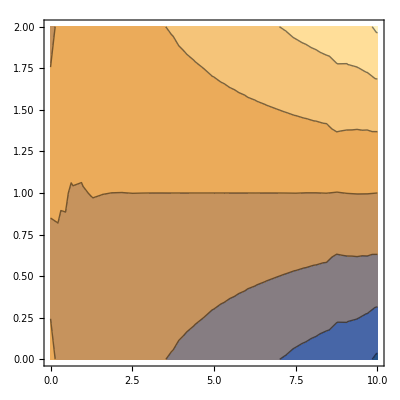

```mathematica
stresslist
```

```mathematica
Flatten[stresslist,3]
```

{{4.80041,4.80041,4.80041},{5.11035,5.11035,5.11035},{5.42029,5.42029,5.42029},{4.80041,4.80041,4.80041},{5.11035,5.11035,5.11035},{5.42029,5.42029,5.42029},{4.80041,4.80041,4.80041},{5.11035,5.11035,5.11035},{5.42029,5.42029,5.42029},{4.74167,4.74167,4.74167},{5.02718,5.02718,5.02718},{5.31269,5.31269,5.31269},{4.74167,4.74167,4.74167},{5.02718,5.02718,5.02718},{5.31269,5.31269,5.31269},{4.74167,4.74167,4.74167},{5.02718,5.02718,5.02718},{5.31269,5.31269,5.31269},{4.68292,4.68292,4.68292},{4.944,4.944,4.944},{5.20508,5.20508,5.20508},{4.68292,4.68292,4.68292},{4.944,4.944,4.944},{5.20508,5.20508,5.20508},{4.68292,4.68292,4.68292},{4.944,4.944,4.944},{5.20508,5.20508,5.20508},{2.30423,2.30423,2.30423},{2.28711,2.28711,2.28711},{2.27,2.27,2.27},{2.30423,2.30423,2.30423},{2.28711,2.28711,2.28711},{2.27,2.27,2.27},{2.30423,2.30423,2.30423},{2.28711,2.28711,2.28711},{2.27,2.27,2.27},{2.00975,2.00975,2.00975},{1.99025,1.99025,1.99025},{1.97075,1.97075,1.97075},{2.00975,2.00975,2.00975},{1.99025,1.99025,1.99025},{1.97075,1.97075,1.97075},{2.00975,2.00975,2.00975},{1.99025,1.99025,1.99025},{1.97075,1.97075,1.97075},{1.71527,1.71527,1.71527},{1.69339,1.69339,1.69339},{1.67151,1.67151,1.67151},{1.71527,1.71527,1.71527},{1.69339,1.69339,1.69339},{1.67151,1.67151,1.67151},{1.71527,1.71527,1.71527},{1.69339,1.69339,1.69339},{1.67151,1.67151,1.67151},{-0.0284856,-0.0284856,-0.0284856},{-0.0357135,-0.0357135,-0.0357135},{-0.0520035,-0.0520035,-0.0520035},{-0.0284856,-0.0284856,-0.0284856},{-0.0357135,-0.0357135,-0.0357135},{-0.0520035,-0.0520035,-0.0520035},{-0.0284856,-0.0284856,-0.0284856},{-0.0357135,-0.0357135,-0.0357135},{-0.0520035,-0.0520035,-0.0520035},{-0.160191,-0.160191,-0.160191},{-0.175195,-0.175195,-0.175195},{-0.197852,-0.197852,-0.197852},{-0.160191,-0.160191,-0.160191},{-0.175195,-0.175195,-0.175195},{-0.197852,-0.197852,-0.197852},{-0.160191,-0.160191,-0.160191},{-0.175195,-0.175195,-0.175195},{-0.197852,-0.197852,-0.197852},{-0.244551,-0.244551,-0.244551},{-0.264496,-0.264496,-0.264496},{-0.290682,-0.290682,-0.290682},{-0.244551,-0.244551,-0.244551},{-0.264496,-0.264496,-0.264496},{-0.290682,-0.290682,-0.290682},{-0.244551,-0.244551,-0.244551},{-0.264496,-0.264496,-0.264496},{-0.290682,-0.290682,-0.290682}}

```mathematica
Flatten[stresslists,3]
```

{{7.5,7.5,7.5},{7.50382,7.50382,7.50382},{7.50764,7.50764,7.50764},{7.5,7.5,7.5},{7.50382,7.50382,7.50382},{7.50764,7.50764,7.50764},9939,{-0.244551,-0.244551,-0.244551},{-0.264496,-0.264496,-0.264496},{-0.290682,-0.290682,-0.290682},{-0.244551,-0.244551,-0.244551},{-0.264496,-0.264496,-0.264496},{-0.290682,-0.290682,-0.290682}}
 |  |  |  |

$Aborted

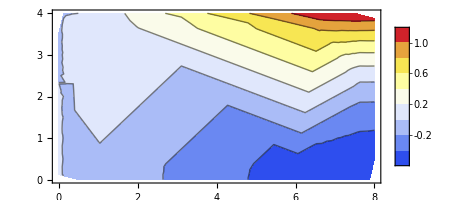

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[(dsols),30 10^6,0.30][[1]];
stresslists={};
sx=1;
refine=0.75;
For[i=1,i≤Length[stress],i++,

stresslist=ParallelTable[{X[[i,1]],X[[i,2]],stress[[i,sx]]},{xi,-1,1,refine},{eta,-1,1,refine}];
AppendTo[stresslists,stresslist];

];
ListContourPlot[Flatten[stresslists,2],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic]
```